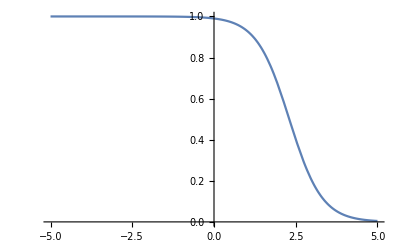

```mathematica
(* Define transformation and plot *)
f[x_,al_,be_]:=1/(1+1/al Exp[be x]);
Plot[f[x,100,2],{x,-5,5}]
```

```mathematica
(* Transformation. Specify the desired range. 0.01 and 0.99 gives bad results *)
lowval = 0.01;
upval = 7/8;
(* original range *)
lowvalor = 100;
upvalor = 600;
subs=FullSimplify[NSolve[{f[lowvalor,al,be]==upval, f[upvalor,al,be]==lowval},{al,be}, Reals]][[1]]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{al→25.8967,be→0.0130821}

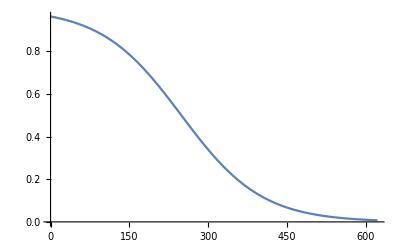

```mathematica
(* Plot transformed values *)
Plot[f[x,al,be]//.subs,{x,0,622}]
```

```mathematica
(* Inverse transformation *)
xrestored=Simplify[Solve[f[x,al,be]==y,x,Reals],Assumptions->{y<1,y>0, al>0}][[1,1]]
```

x→Log[al (-1+1/y)]/be

```mathematica
(* Check inverse transformation *)
xval = 0.51;
xval - (x//.(xrestored//.(y->f[xval,al,be]//.subs)//.subs))
```

-1.35669×10^-13